# Coordinates

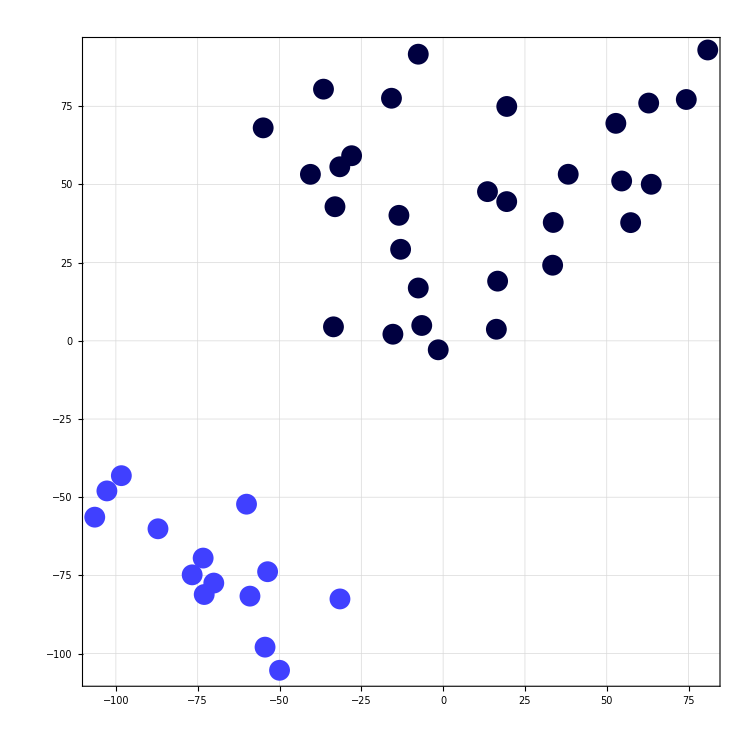

```mathematica
coordinates=Import["ATaleOfTwoCitiesScaled_Coordinates.csv"];
clusters=FindClusters[coordinates];
ListPlot[clusters
,AspectRatio->1
,AxesOrigin->{Min[coordinates[[All,1]]],Min[coordinates[[All,1]]]}
,Frame->True
,FrameStyle->Thick
,FrameTicksStyle->Directive[20]
,GridLines->Automatic
,GridLinesStyle->Directive[Thick,Opacity[.1]]
,ImageSize->750
,PlotStyle->(Directive[#,Opacity[1],EdgeForm[Black],PointSize[.02]]&/@{Darker[Blue,.75],Lighter[Blue,.25]})
]
```

# Heat Map

/Users/sanchez.hmsc/Documents/GitHub/dataViz_CADi/scripts/Transitions

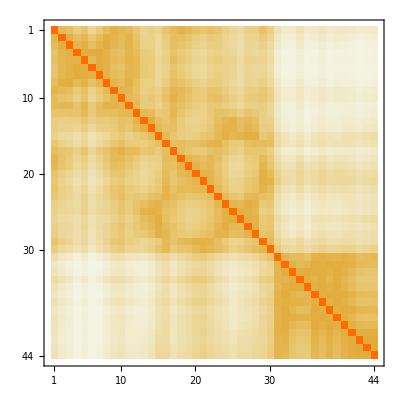

```mathematica
SetDirectory[NotebookDirectory[]]
rawData=Import["ATaleOfTwoCitiesScaled_Kernel.csv"];
MatrixPlot[rawData]
```

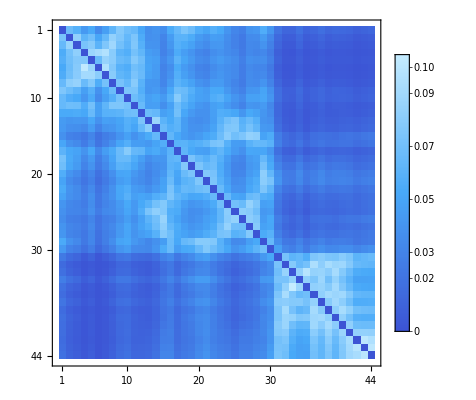

```mathematica
zeroDiagonal=ReplacePart[rawData,{i_,i_}->0];
MatrixPlot[zeroDiagonal*100
,ColorFunction->"DeepSeaColors"
,FrameStyle->Thick
,PlotLegends->Automatic
]
```

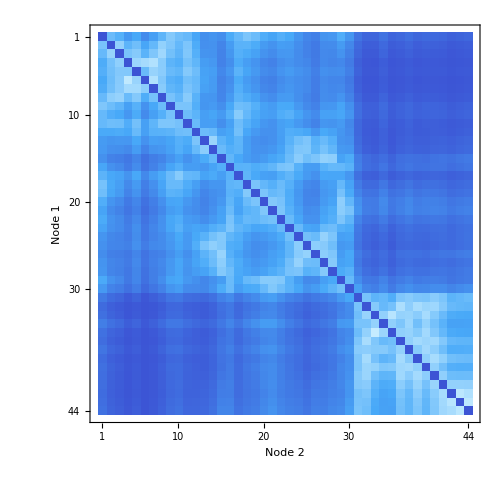
-Graphics- |  |

transitions.pdf

```mathematica
scaledDiagonal=zeroDiagonal*100;
matrix=MatrixPlot[scaledDiagonal
,ColorFunction->"DeepSeaColors"
,FrameLabel->(Style[#,30]&/@{"Node 1","Node 2"})
,FrameTicksStyle->Directive[15]
,FrameStyle->Thick
,ImageSize->500
,PlotRangePadding->0
];
matrixBar=BarLegend[{"DeepSeaColors",{0,scaledDiagonal//Flatten//Max}},
LabelStyle->15,
LegendLabel->Style["Migration\nProbability x10",20],
LegendMarkerSize->250
];
Grid[{{matrix,"",matrixBar}}]
Export["transitions.pdf",%]
```